```mathematica
SetDirectory["~/code/rule146"]
```

/Users/rule146/code/rule146

```mathematica
FileNames["*"]
```

{.git,Kernel,NKS.m,ProjectUtilities.m,README.md,Rule146.m}

```mathematica
<<Rule146`
```

```mathematica
<<ProjectUtilities`
```

```mathematica
<<NKS`
```

HighlightEvenRuns::shdw: Symbol "HighlightEvenRuns" appears in multiple contexts {"NKS`", "Rule146`"}; definitions in context "NKS`" may shadow or be shadowed by other definitions.

aph::shdw: Symbol "aph" appears in multiple contexts {"NKS`", "Rule146`"}; definitions in context "NKS`" may shadow or be shadowed by other definitions.

```mathematica
Names["Rule146`*"]
```

{Rule146`aph,Rule146`HighlightEvenRuns}

```mathematica
Names["ProjectUtilities`*"]
```

{CreateProjectNotebook}

```mathematica
Names["NKS`*"]
```

{AllRepeatingBackgrounds,aph,ApplyDefect,CyclicUnion,HighlightEvenRuns,PadAround,SearchForBackgroundsOfLengthStepRepeat}

```mathematica
Remove["NKS`*"]
```

## create initial conditions with exactly one even run

```mathematica
ParticleInit[length_]:=RotateRight[Riffle[RandomInteger[1,Ceiling[length/2]],0],Floor[length/2]]
```

```mathematica
Length@ParticleInit[49]
```

49

```mathematica
Length/@Split[ParticleInit[50]]
```

{1,1,1,3,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,3,1,5,1,7,1,1,1,1}

```mathematica
aph[HighlightEvenRuns/@CellularAutomaton[146,ParticleInit[100],300]]
```

-Graphics-

```mathematica
Table[aph[HighlightEvenRuns/@CellularAutomaton[146,ParticleInit[100],300]],{10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## distribution of paths of a single particle

```mathematica
Union[Flatten[HighlightEvenRuns/@CellularAutomaton[146,ParticleInit[100],300]]]
```

{0,1,2,3}

```mathematica
init=ParticleInit[100]
```

{0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,1,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,1,0,1,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0}

```mathematica
HighlightEvenRuns@init
```

{0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,1,0,0,0,0,0,1,0,0,0,1,2,2,2,2,2,2,2,2,2,2,2,2,1,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,1,0,1,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0}

```mathematica
HighlightEvenRuns@init/.{1->0,2->1,3->1}
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Plus@@Table[HighlightEvenRuns@ParticleInit[100]/.{1->0,2->1,3->1},{10}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,2,2,2,2,2,4,8,6,3,3,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
aph[{Plus@@Table[HighlightEvenRuns@ParticleInit[49]/.{1->0,2->1,3->1},{10}]/10.},10,Mesh->All]
```

-Graphics-

```mathematica
Plus[{{1,0},{1,0}},{{1,0},{1,0}}]
```

{{2,0},{2,0}}

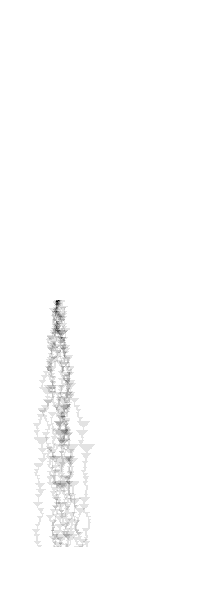

```mathematica
ArrayPlot[Plus@@Table[ReplaceAll[HighlightEvenRuns/@CellularAutomaton[146,ParticleInit[100],300],{1->0,2->1,3->1}],{10}]/10.,PixelConstrained->2]
```

```mathematica
ensemble=Table[ReplaceAll[HighlightEvenRuns/@CellularAutomaton[146,ParticleInit[100],300],{1->0,2->1,3->1}],{100}];//AbsoluteTiming
```

{5.58339,Null}

(HighlightEvenRuns needs to be sped up.)

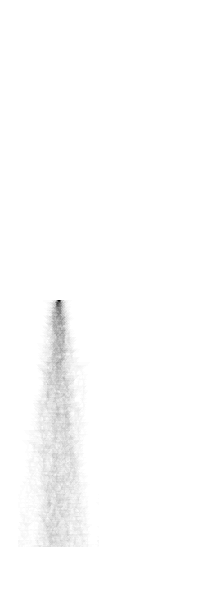

```mathematica
ArrayPlot[Plus@@ensemble/100.,PixelConstrained->2]
```

### If the particle is doing a random walk, expect to see a diffusion outwards from the center

### But does the particle have “path memory”? And if so, does this cause some bias in the available positions? i.e. how do past positions effect future ones?

### Show a correlation map: when particle visits (x,t), how often does it also visit (x+a, t+delta) after delta timesteps in the same run?

### Path distribution shows the correlation map between (x,t) = (l/2, 0) and all other (x, 0 + delta) for delta = 1,2,3, ... because the particle always visits (l/2, 0) by construction

## path memory for a single particle

```mathematica
Length@ParticleInit[100]
```

99

### distribution of paths that go through (x,t) = (50, 50)

```mathematica
Length@Select[ensemble,#[[50,50]]==1&]
```

19

```mathematica
Select[ensemble,#[[50,50]]==1&]
```

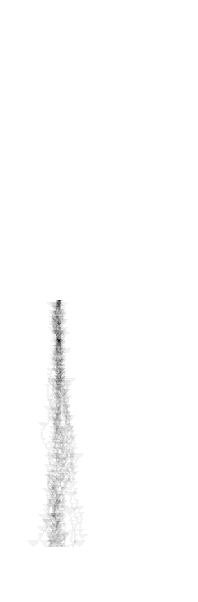

```mathematica
With[{subensemble=Select[ensemble,#[[50,50]]==1&]},
ArrayPlot[Plus@@subensemble/N@Length@subensemble,PixelConstrained->2]
]
```

### need better stats, so need more runs that visit (50, 50)

### so HighlightEvenRuns needs to be sped up a lot

```mathematica
ListConvolve[{1,1},{0,1,0,1,0,0,1,1,0,0,0,1,0,0,0},1]
```

{0,1,1,1,1,0,1,2,1,0,0,1,1,0,0}

```mathematica
{0,1,0,1,0,0,1,1,0,0,0,1,0,0,0}
```

```mathematica
{0,1,1,1,1,0,1,2,1,0,0,1,1,0,0}
```

```mathematica
ListConvolve[{1,0,0,0,0,1},{0,1,0,1,0,0,1,1,0,0,0,1,0,0,0},1]
```

{0,2,0,1,0,0,2,1,1,0,0,2,1,0,0}

```mathematica
1-{0,1,0,1,0,0,1,1,0,0,0,1,0,0,0}
```

{1,0,1,0,1,1,0,0,1,1,1,0,1,1,1}

```mathematica
ListConvolve[{1,1},1-{0,1,0,1,0,0,1,1,0,0,0,1,0,0,0},1]
```

{2,1,1,1,1,2,1,0,1,2,2,1,1,2,2}

```mathematica
{0,1,0,1,0,0,1,1,0,0,0,1,0,0,0}
```

```mathematica
{2,1,1,1,1,2,1,0,1,2,2,1,1,2,2}
```

## interference of two particles

## what is the probabilistic rule that gives the same path distribution?